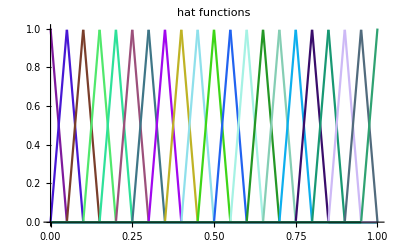

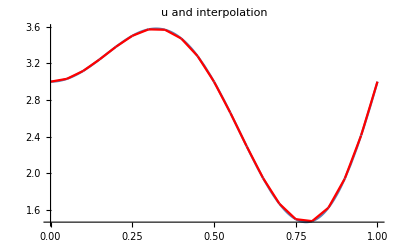

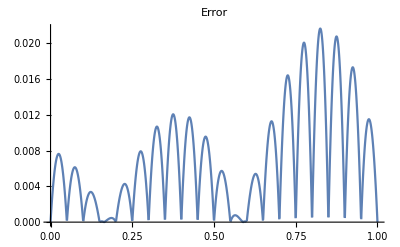

0.00874337

0.439738

```mathematica
hat[i_Integer,points_List, x_]:=
Which[
i≥2&&i≤Length[points]-1,
Piecewise[{{(x-points⟦i-1⟧)/(points⟦i⟧-points⟦i-1⟧), points⟦i-1⟧≤x≤points⟦i⟧}, {(points⟦i+1⟧-x)/(points⟦i+1⟧-points⟦i⟧), points⟦i⟧≤x≤points⟦i+1⟧}, {0, True}}],
i==1,
Piecewise[{{(points⟦i+1⟧-x)/(points⟦i+1⟧-points⟦i⟧), points⟦i⟧≤x≤points⟦i+1⟧}, {0, True}}],
i==Length[points],
Piecewise[{{(x-points⟦i-1⟧)/(points⟦i⟧-points⟦i-1⟧), points⟦i-1⟧≤x≤points⟦i⟧}, {0, True}}]
]

n=20;
minX = 0;
maxX = 1;
points = Table[minX + k maxX/n,{k,0,n}];
colors = RandomColor@Length[points];
Show[
Table[
Plot[hat[i, points, x],{x,First[points],Last[points]}, PlotRange->All,PlotLegends->"Expressions", PlotStyle-> colors⟦i⟧],
{i,1,Length[points]}],
 PlotLabel-> "hat functions"]

u[x_]:=2 x Sin[2 Pi x]+3

hatInterpolate[u_,points_List, x_]:=∑_(i=1)^Length[points] u[points⟦i⟧]hat[i, points, x]
interpolationError[u_,points_List,x_]:=u[x]-hatInterpolate[u, points, x]

Show[
{Plot[u[x],{x,First[points],Last[points]}, PlotRange->All]},
{Plot[hatInterpolate[u, points, x],{x,First[points],Last[points]}, PlotRange->All,PlotStyle->Red]},
PlotLabel->"u and interpolation"
]

maxStep[points_List]:=Max@Differences[points]

L2Norm[u_,a_,b_]:=√NIntegrate[u[x]^2,{x,a,b}]
aprioriErrorEstimate[u_,points_List]:= √Length[points] L2Norm[u'',First[points],Last[points]] maxStep[points]^2  
errorNorm[u_,points_List]:=√NIntegrate[interpolationError[u,points,x]^2,{x,First[points],Last[points]}]

Plot[Abs@interpolationError[u,points,x],{x,First[points],Last[points]}, PlotLabel->"Error"]


errorNorm[u,points]
aprioriErrorEstimate[u,points]
```